```mathematica
$Assumptions = {t∈Reals, t≥0, tr∈Reals, tr>0, t≤ tr, 
a∈ Reals, b∈Reals, a>0, b>0, a< 1/2,  b< 1/2,  a+b <1/2, 
m∈Integers};
```

```mathematica
wnut = Piecewise[{
{(4 π)/(b tr), a tr ≤t < (a+b/8)tr },
{-(4 π)/(b tr), (a+b/8)tr≤t < (a+(5b)/8)tr},
{(4 π)/(b tr), (a+(5b)/8)tr≤t < (a+b)tr},
{(4 π)/(b tr), tr-(a+b)tr ≤t < tr-(a+(5b)/8)tr },
{-(4 π)/(b tr),  tr-(a+(5b)/8)tr≤t <  tr-(a+b/8)tr},
{(4 π)/(b tr), tr-(a+b/8)tr≤t <  tr-a tr }
}];
```

```mathematica
brf[t_] = ∫_0^t wnutⅆt //FullSimplify
```

Piecewise[{{(π (-4 t+(4 a+b) tr))/(b tr), 8 a tr+5 b tr≥8 t&&(8 a+b) tr<8 t}, {(4 π (t-a tr))/(b tr), a tr<t&&(8 a+b) tr≥8 t}, {(4 π (t-(a+b) tr))/(b tr), (a+b) tr≥t&&8 a tr+5 b tr<8 t}, {-(π (4 t+(-4+4 a+b) tr))/(b tr), 8 t+8 a tr+5 b tr>8 tr&&8 t+(-8+8 a+b) tr≤0}, {(4 π (t+(-1+a) tr))/(b tr), 8 t+(-8+8 a+b) tr>0&&t+a tr≤tr}, {(4 π (t+(-1+a+b) tr))/(b tr), 8 t+8 a tr+5 b tr≤8 tr&&t+(a+b) tr>tr}, {0, True}}]

```mathematica
brf[t_] =Piecewise[{{(π (-4 t+(4 a+b) tr))/(b tr), 8 a tr+5 b tr≥8 t&&(8 a+b) tr<8 t}, {(4 π (t-a tr))/(b tr), a tr<t&&(8 a+b) tr≥8 t}, {(4 π (t-(a+b) tr))/(b tr), (a+b) tr≥t&&8 a tr+5 b tr<8 t}, {-(π (4 t+(-4+4 a+b) tr))/(b tr), 8 t+8 a tr+5 b tr>8 tr&&8 t+(-8+8 a+b) tr≤0}, {(4 π (t+(-1+a) tr))/(b tr), 8 t+(-8+8 a+b) tr>0&&t+a tr≤tr}, {(4 π (t+(-1+a+b) tr))/(b tr), 8 t+8 a tr+5 b tr≤8 tr&&t+(a+b) tr>tr}, {0, True}}];
```

```mathematica
Chilm[l_,  m_, λ_, μ_] := 1/tr∫_0^tr WignerD[{λ, μ, 0}, - brf[t] ]Exp[ⅈ (μ π/2 +m  t (2π/tr))]ⅆt
```

#### Plot Function

```mathematica
PlotFunc[f1_, f2_, f3_, f4_]:=
Module[{p1, p2, p3},
p1 = ContourPlot[f1[a, b], {a, 0, 1/2},{b, 0, 1/2},
ContourLines->False,
PlotRange -> {-0.5, 0.5},
RegionFunction-> Function[{a, b}, a+b<1/2],
PerformanceGoal->"Quality",
Axes->True,Frame->False,
ColorFunction->(ColorData[{"ThermometerColors",{-0.5,0.5}}]),
ColorFunctionScaling->False,
AxesStyle->{Thick},
PlotLabel-> f1,
AxesLabel->{a, b}
];
p2 = ContourPlot[f1[a, b]==f2[a, b],
{a, 0, 1/2},{b, 0, 1/2},
ContourStyle->{Black, Thick},
RegionFunction-> Function[{a, b}, a+b<1/2],
Axes->True,Frame->False, AxesStyle->{Thick}
];
p3 = ContourPlot[f3[a, b]==f4[a, b],
{a, 0, 1/2},{b, 0, 1/2},
ContourStyle->{Black, Thick, Dashed},
RegionFunction-> Function[{a, b}, a+b<1/2],
Axes->True,Frame->False, AxesStyle->{Thick}];
Show[p1, p2, p3]
]
```

#### CSA

```mathematica
Chi2110[a_, b_] =  Chilm[2, 1, 1, 0]//  TrigToExp// FullSimplify
```

(4 (-b Cos[1/4 (8 a+b) π]+b Cos[2 a π+(5 b π)/4]-Sin[2 a π]+Sin[2 (a+b) π]))/((-4+b^2) π)

```mathematica
Chi2110[a_, b_] = (4 (-b Cos[1/4 (8 a+b) π]+b Cos[2 a π+(5 b π)/4]-Sin[2 a π]+Sin[2 (a+b) π]))/((-4+b^2) π);
```

```mathematica
Chi2111[a_, b_] =  Chilm[2, 1, 1, 1]//  TrigToExp// FullSimplify
```

```mathematica
Chi2111[a_, b_] =(2 √2 b Cos[(2 a+b) π] Sin[b π])/((-4+b^2) π);
```

(2 √2 b Cos[(2 a+b) π] Sin[b π])/((-4+b^2) π)

```mathematica
Chi2111[0.0329, 0.467]
```

0.0113741

```mathematica
Chi211n1[a_, b_] =  Chilm[2, 1, 1, -1]//  TrigToExp// FullSimplify
```

(2 √2 b Cos[(2 a+b) π] Sin[b π])/((-4+b^2) π)

```mathematica
Chi12[a_, b_] =  Chilm[1, 2]//  TrigToExp// FullSimplify
```

(Sin[b π] (Cos[(4 a+b) π]+Cos[4 a π+3 b π]-2 b Sin[4 a π+(3 b π)/2]))/((-1+b^2) π)

```mathematica
Chi12[a_, b_] = (Sin[b π] (Cos[(4 a+b) π]+Cos[4 a π+3 b π]-2 b Sin[4 a π+(3 b π)/2]))/((-1+b^2) π);
```

```mathematica
Reduce[Chi12[a, b]== {a, b}&&0<a<1/2&&0<b<1/2, {a, b}, Reals]
```

#### DD

```mathematica
Chi21[a_, b_] =  Chilm[2, 1]//  TrigToExp// FullSimplify
```

Piecewise[{{(-12 Sin[2 a π]+(-4+b^2) Sin[2 (a+b) π])/((-4+b) (4+b) π), a+b≥1/2}, {(24 Cos[(2 a+b) π] Sin[b π])/((-16+b^2) π), True}}]

```mathematica
Chi21[a_, b_] =(24 Cos[(2 a+b) π] Sin[b π])/((-16+b^2) π);
```

```mathematica
Chi22[a_, b_] =  Chilm[2, 2]//  TrigToExp// FullSimplify
```

Piecewise[{{(-3 Sin[4 a π]+(-1+b^2) Sin[4 (a+b) π])/(2 (-4+b^2) π), a+b≥1/2}, {(3 Cos[2 (2 a+b) π] Sin[2 b π])/((-4+b^2) π), True}}]

```mathematica
Chi22[a_, b_]=(3 Cos[2 (2 a+b) π] Sin[2 b π])/((-4+b^2) π);
```

```mathematica
Chi2121[a_, b_] =  Chilm[2, 1, 2, 1]//  TrigToExp// FullSimplify
```

```mathematica
Chi2121[a_, b_] =(√6 b (-Sin[2 a π]+Sin[2 (a+b) π]-2 Sin[1/4 (8 a+b) π]+2 Sin[2 a π+(5 b π)/4]))/((-4+b) (4+b) π);
```

```mathematica
Chi2120[0.035, 0.467]
```

-0.00999622

```mathematica
Chi2122[a_, b_] =  Chilm[2, 1, 2, 2]//  TrigToExp// FullSimplify
```

```mathematica
Chi2122[a_, b_] =(4 √6 Cos[(2 a+b) π] Sin[b π])/((-16+b^2) π);
```

```mathematica
Chi2122[0.0327, 0.467]
```

0.0199725

```mathematica
Chi2221[a_, b_] =  Chilm[2, 2, 2, 1]//  TrigToExp// FullSimplify
```

```mathematica
Chi2221[a_, b_] =(√(3/2) b (-Sin[4 a π]+Sin[4 (a+b) π]-2 Sin[1/2 (8 a+b) π]+2 Sin[4 a π+(5 b π)/2]))/(2 (-4+b^2) π);
```

```mathematica
Chi2221[0.0327, 0.467]
```

0.0923303

```mathematica
Chi2n221[a_, b_] =  Chilm[2, -2, 2, 1]//  TrigToExp// FullSimplify
```

(√(3/2) b (Sin[4 a π]-Sin[4 (a+b) π]+2 Sin[1/2 (8 a+b) π]-2 Sin[4 a π+(5 b π)/2]))/(2 (-4+b^2) π)

```mathematica
Chi2222[a_, b_] =  Chilm[2, 2, 2, 2]//  TrigToExp// FullSimplify
```

```mathematica
Chi2222[a_, b_] =(√(3/2) Cos[2 (2 a+b) π] Sin[2 b π])/((-4+b^2) π);
Chi2222[0.0327, 0.467]
```

0.0207826

#### Plots

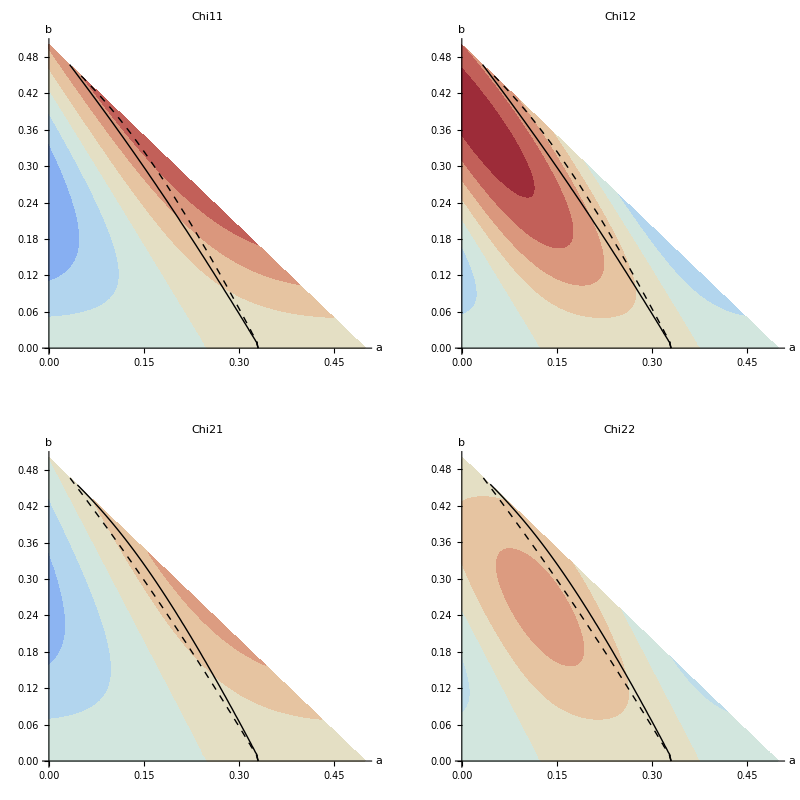

```mathematica
s1 = PlotFunc[Chi11, Chi12, Chi21, Chi22];
s2 = PlotFunc[Chi12, Chi11, Chi21, Chi22];
s3 = PlotFunc[Chi21, Chi22, Chi11, Chi12];
s4 = PlotFunc[Chi22, Chi21, Chi11, Chi12];
GraphicsGrid[{{s1, s2},{s3, s4}}]
```